```mathematica
SetOptions[Plot,BaseStyle->Directive@@{FontColor->Black},TicksStyle->Directive@@{FontColor->Black},LabelStyle->Directive@@{FontColor->Black}];
```

```mathematica
trapezoidal[x_]:=Module[{},
If[x<30,x/30,
If[x<150,1,
If[x<210,-(x-180)/30,
If[x<330,-1,
If[x<390,(x-360)/30,1]]]]]
];
angularTicks={0,60,120,180,240,300,360,420,480};
Plot[{Sin[x °],trapezoidal[x]},{x,0,510},
PlotTheme->"Detailed",
PlotRange->All,
FrameLabel->{"Electrical position, angular degrees","Back EMF"},
PlotLegends->Placed[LineLegend[{"Sinusoidal BEMF","Trapezoidal BEMF"},LegendLayout->"Row"],{Center,0}],
ImageSize->Medium,
FrameTicks->{angularTicks,Automatic},
GridLines->{angularTicks,Automatic}]
```

-Graphics-

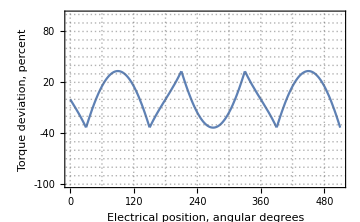

```mathematica
Plot[{(Sin[x °]/0.75-trapezoidal[x])100},{x,0,510},
PlotTheme->"Detailed",
PlotLegends->None,
PlotRange->{Automatic,{-100,100}},
FrameLabel->{"Electrical position, angular degrees","Torque deviation, percent"},
ImageSize->Medium,
FrameTicks->{angularTicks,Table[i,{i,-100,100,20}]},
GridLines->{angularTicks,Table[i,{i,-100,100,10}]}]
```